# A particle on a six-site ring: symmetry becomes a spectrum

Consider one particle that can occupy six equivalent sites around a ring and hop to either neighbor. Why do waves appear as its energy eigenstates? What happens if we start at one specific site, or otherwise make that site different?

Connections to SMSA v7.7: §1.5, ‘Order of a group and of group elements’; §1.9, ‘Generators and relations’; §3.1, ‘Algebras’, especially the group-algebra construction (3.11)–(3.15); §4.2, ‘Group representations’; §4.3, ‘Trivial and regular representations’; and §4.4, ‘Reducibility’. The hopping Hamiltonian is a physical application of these concepts.

We assume a single particle, periodic boundary conditions and equal real hopping energy J>0 in the two directions. (Adding magnetic flux is a natural generalization, but we don’t consider it here.) Site labels run from 0 to 5, while Mathematica list positions run from 1 to 6. CTime plots use the dimensionless variable τ==(J t)/ℏ.

## 1. Positions and a one-step translation

```mathematica
Remove["Global`*"] //Quiet
nSites=6;siteLabels=Range[0,nSites-1];siteBasis=IdentityMatrix[nSites];positions=Table[{Cos[2π j/nSites],Sin[2π j/nSites]},{j,0,nSites-1}];
```

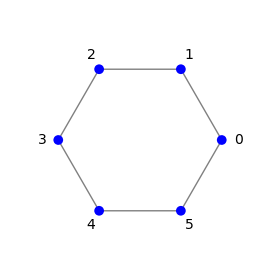

```mathematica
ringDiagram=Graphics[{Gray,Thick,Line[Append[positions,First[positions]]],Blue,PointSize[0.025],Point[positions],Black,Table[Text[Style[j,14],1.2 positions〚j+1〛],{j,0,nSites-1}]},PlotRange{{-1.4,1.4},{-1.4,1.4}},ImageSize280]
```

The vector {1,0,0,0,0,0} means that the particle is at site 0. A one-step translation moves each site to the next, with site 5 returning to site 0. Put the image of each basis vector into a column.

```mathematica
shift=Transpose[Table[UnitVector[nSites,Mod[j+1,nSites]+1],{j,0,nSites-1}]]
```

(0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0)

```mathematica
{shift.siteBasis⟦1⟧,shift.siteBasis⟦6⟧,MatrixPower[shift,nSites]==IdentityMatrix[nSites]}
```

{{0,1,0,0,0,0},{1,0,0,0,0,0},True}

Six steps give the identity: T^6=I_6. The six powers of T form a representation of the cyclic group. This is its regular representation: group elements shift the six site labels.

Six one-step translations return every site to its starting position.

```mathematica
MatrixPower[shift,nSites]IdentityMatrix[nSites]
```

True

## 2. A Hamiltonian built from group elements

Allow the particle to hop one step in either direction, with amplitude −J. The Hamiltonian is H==-J (T^-1+T). Since T is a real permutation matrix, its inverse is its transpose.

```mathematica
hamiltonian=-J (shift+Transpose[shift]);hamiltonian
```

(0 | -J | 0 | 0 | 0 | -J
-J | 0 | -J | 0 | 0 | 0
0 | -J | 0 | -J | 0 | 0
0 | 0 | -J | 0 | -J | 0
0 | 0 | 0 | -J | 0 | -J
-J | 0 | 0 | 0 | -J | 0)

Each column shows which neighboring sites are coupled to an input site. A Hamiltonian is a linear operator with energy units, not a translation. Here it is a linear combination of represented group elements: a concrete use of the group algebra in §3.1.

```mathematica
{FullSimplify[ConjugateTranspose[hamiltonian]==hamiltonian,J∈Reals],Simplify[hamiltonian.shift-shift.hamiltonian]==ConstantArray[0,{nSites,nSites}]}
```

{True,True}

Translation commutes with the Hamiltonian, so we can look for states that have both a definite translation phase and a definite energy. This is more informative than asking for eigenvectors without using the symmetry.

For real J, the hopping Hamiltonian is Hermitian.

```mathematica
FullSimplify[ConjugateTranspose[hamiltonian]hamiltonian,J∈Reals]
```

True

Translation is a symmetry: translating before or after applying the Hamiltonian gives the same result.

```mathematica
Simplify[hamiltonian.shift-shift.hamiltonian]ConstantArray[0,{nSites,nSites}]
```

True

## 3. Let the phase advance equally from site to site

A wave that closes around the ring can have phase increment k_m==(2 π m)/6, with m=0,…,5. Its amplitude at site j is (exp(ⅈ j k_m))/(√6). The normalization makes the sum of the six site probabilities one.

```mathematica
waveNumbers=(2 π siteLabels)/nSites;fourier=Table[Exp[ⅈ waveNumbers⟦m+1⟧ j]/(√nSites),{j,0,nSites-1},{m,0,nSites-1}]
FullSimplify[ConjugateTranspose[fourier].fourier]
```

(1/(√6) | 1/(√6) | 1/(√6) | 1/(√6) | 1/(√6) | 1/(√6)
1/(√6) | ⅇ^((ⅈ π)/3)/(√6) | ⅇ^((2 ⅈ π)/3)/(√6) | -1/(√6) | ⅇ^(-(2 ⅈ π)/3)/(√6) | ⅇ^(-(ⅈ π)/3)/(√6)
1/(√6) | ⅇ^((2 ⅈ π)/3)/(√6) | ⅇ^(-(2 ⅈ π)/3)/(√6) | 1/(√6) | ⅇ^((2 ⅈ π)/3)/(√6) | ⅇ^(-(2 ⅈ π)/3)/(√6)
1/(√6) | -1/(√6) | 1/(√6) | -1/(√6) | 1/(√6) | -1/(√6)
1/(√6) | ⅇ^(-(2 ⅈ π)/3)/(√6) | ⅇ^((2 ⅈ π)/3)/(√6) | 1/(√6) | ⅇ^(-(2 ⅈ π)/3)/(√6) | ⅇ^((2 ⅈ π)/3)/(√6)
1/(√6) | ⅇ^(-(ⅈ π)/3)/(√6) | ⅇ^(-(2 ⅈ π)/3)/(√6) | -1/(√6) | ⅇ^((2 ⅈ π)/3)/(√6) | ⅇ^((ⅈ π)/3)/(√6))

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

The columns are the six waves. Our (active) translation shifts the amplitudes one site forward; this gives the phase with a minus sign. Check the convention instead of guessing it:

```mathematica
translationPhases=FullSimplify[Exp[-ⅈ waveNumbers]];FullSimplify[ConjugateTranspose[fourier].shift.fourier==DiagonalMatrix[translationPhases]]
```

True

Each one-dimensional wave space is invariant under translation. We have decomposed the six-dimensional regular representation into six one-dimensional complex representations, as discussed for finite abelian groups in §4.4.16.

The Fourier columns form an orthonormal basis.

```mathematica
ConjugateTranspose[fourier].fourier
```

(1 | 1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 0 | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3)
1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 1 | 1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 1/3-1/6 ⅇ^(-(ⅈ π)/3)-1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 0 | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3)
1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 1 | 0 | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 0
0 | 1/3-1/6 ⅇ^(-(ⅈ π)/3)-1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 0 | 1 | 0 | 1/3-1/6 ⅇ^(-(ⅈ π)/3)-1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3)
1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 0 | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 0 | 1 | 1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3)
1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 0 | 1/3-1/6 ⅇ^(-(ⅈ π)/3)-1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 1)

```mathematica
Simplify[%==IdentityMatrix[nSites]]
```

True

In the Fourier basis, translation has the phases given above.

```mathematica
ConjugateTranspose[fourier].shift.fourier
```

(1 | 1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 0 | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3)
1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | 2/3 ⅇ^(-(ⅈ π)/3)-1/3 ⅇ^((2 ⅈ π)/3) | 1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | -1/3+1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)-1/6 ⅇ^(-(2 ⅈ π)/3)-1/6 ⅇ^((2 ⅈ π)/3) | 1/3 ⅇ^(-(ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | -1/3+1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)-1/6 ⅇ^(-(2 ⅈ π)/3)-1/6 ⅇ^((2 ⅈ π)/3)
1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3) | 0 | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1/3 ⅇ^((ⅈ π)/3)+1/3 ⅇ^(-(2 ⅈ π)/3)
0 | -1/3+1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)-1/6 ⅇ^(-(2 ⅈ π)/3)-1/6 ⅇ^((2 ⅈ π)/3) | 0 | -1 | 0 | -1/3+1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)-1/6 ⅇ^(-(2 ⅈ π)/3)-1/6 ⅇ^((2 ⅈ π)/3)
1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1/3 ⅇ^(-(ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 1/3+1/3 ⅇ^(-(2 ⅈ π)/3)+1/3 ⅇ^((2 ⅈ π)/3) | 0 | ⅇ^((2 ⅈ π)/3) | 1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)
1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3)+1/6 ⅇ^((2 ⅈ π)/3) | -1/3+1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)-1/6 ⅇ^(-(2 ⅈ π)/3)-1/6 ⅇ^((2 ⅈ π)/3) | 1/3 ⅇ^((ⅈ π)/3)+1/3 ⅇ^(-(2 ⅈ π)/3) | -1/3+1/6 ⅇ^(-(ⅈ π)/3)+1/6 ⅇ^((ⅈ π)/3)-1/6 ⅇ^(-(2 ⅈ π)/3)-1/6 ⅇ^((2 ⅈ π)/3) | 1/6 ⅇ^((ⅈ π)/3)+1/6 ⅇ^(-(2 ⅈ π)/3) | 2/3 ⅇ^((ⅈ π)/3)-1/3 ⅇ^(-(2 ⅈ π)/3))

```mathematica
Simplify[%==DiagonalMatrix[translationPhases]]
```

True

## 4. Read off the energies

```mathematica
energies=FullSimplify[-2 J Cos[waveNumbers]]
energyMatrix=FullSimplify[ConjugateTranspose[fourier].hamiltonian.fourier]
```

{-2 J,-J,J,2 J,J,-J}

(-2 J | 0 | 0 | 0 | 0 | 0
0 | -J | 0 | 0 | 0 | 0
0 | 0 | J | 0 | 0 | 0
0 | 0 | 0 | 2 J | 0 | 0
0 | 0 | 0 | 0 | J | 0
0 | 0 | 0 | 0 | 0 | -J)

The result is ⅇ_m==-2 J cos(k_m). For J>0 the uniform wave has the lowest energy. The modes m and 6−m have equal energies because the hopping is equal in the two directions. Cyclic symmetry alone does not require these pairs to have equal energies; this Hamiltonian also has reflection symmetry.

```mathematica
energyUnits=Simplify[energies/J];Transpose[{siteLabels,waveNumbers,energyUnits}]
```

(0 | 0 | -2
1 | π/3 | -1
2 | (2 π)/3 | 1
3 | π | 2
4 | (4 π)/3 | 1
5 | (5 π)/3 | -1)

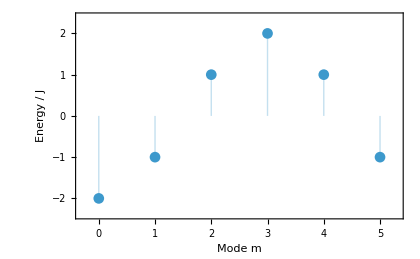

```mathematica
spectrumPlot=ListPlot[Transpose[{siteLabels,energyUnits}],PlotMarkers->Automatic,Filling->Axis,Frame->True,FrameLabel->{"Mode m","Energy / J"},PlotRange->{{-0.3,5.3},{-2.4,2.4}},ImageSize->420];spectrumPlot
```

The Fourier waves diagonalize the Hamiltonian, with the stated energies.

```mathematica
energyMatrixDiagonalMatrix[energies]
```

True

In units of J, the six energies in wave-number order are -2, -1, 1, 2, 1 and -1.

```mathematica
energyUnits{-2,-1,1,2,1,-1}
```

True

## 5. Start with the particle at one site

A state localized at site 0 is a superposition of all six waves. Each wave then acquires its own energy-dependent phase. Interference between those phases changes the site probabilities.

```mathematica
initial=siteBasis⟦1⟧;waveCoefficients=FullSimplify[ConjugateTranspose[fourier].initial];waveCoefficients
```

{1/(√6),1/(√6),1/(√6),1/(√6),1/(√6),1/(√6)}

Time evolution multiplies the mth wave coefficient by exp(-(ⅈ ⅇ_m t)/ℏ). Using τ==(J t)/ℏ, only the energies in units of J are needed. The next function returns the six probabilities, in site order 0,…,5.

```mathematica
stateAt[time_]:=N[fourier].(Exp[-ⅈ N[energyUnits] time] N[waveCoefficients]);probabilityAt[time_]:=Chop[Abs[stateAt[time]]^2];probabilityAt[0]
```

{1.,0,0,0,0,0}

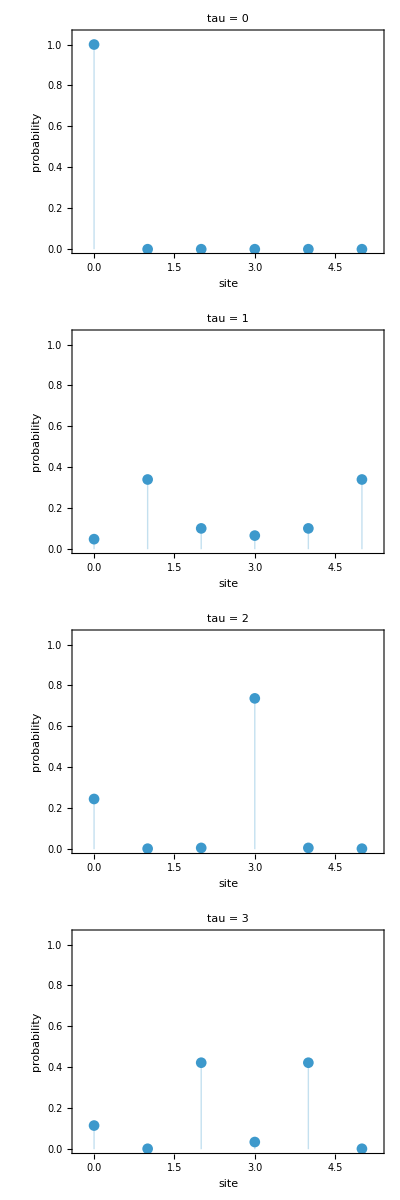

```mathematica
probabilityPlot[values_,caption_]:=ListPlot[Transpose[{siteLabels,values}],Filling->Axis,PlotMarkers->Automatic,PlotRange->{{-0.3,5.3},{0,1.05}},Frame->True,FrameLabel->{"site","probability"},PlotLabel->caption,ImageSize->360];probabilitySnapshots=Column[Table[probabilityPlot[probabilityAt[time],"tau = "time],{time,{0,1,2,3}}]];probabilitySnapshots
```

Change the time slider to watch the particle spread and interfere around the ring. The plotted heights are probabilities, not amplitudes; their sum stays one. The time variable is dimensionless, so a larger hopping energy means faster dynamics in physical time.

At time zero, the particle is entirely at site 0.

```mathematica
probabilityAt[0]N[initial]
```

True

The total probability stays within 10^-12 of one at times from 0 to 12 in steps of 1/4.

```mathematica
Max[Abs[Table[Total[probabilityAt[time]]-1,{time,0,12,1/4}]]]<1/10^12
```

True

## 6. Make one site different

Add an on-site energy V at site 0. Its matrix is zero except for the first diagonal entry: H(V)==H(0)+P_0 V. This changes the physical model and breaks one-step translation symmetry. It need not remove every other symmetry.

```mathematica
site0Projector=Outer[Times,initial,initial];defectiveHamiltonian=hamiltonian+defectEnergy site0Projector;defectCommutator=Simplify[defectiveHamiltonian.shift-shift.defectiveHamiltonian];defectCommutator
```

(0 | 0 | 0 | 0 | 0 | defectEnergy
-defectEnergy | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

For a nonzero defect the displayed commutator is nonzero. Fourier waves no longer diagonalize the Hamiltonian. Compare the two spectra for a defect of energy 2J, using J as the energy unit.

```mathematica
h0=N[hamiltonian/J];hDefect=h0+2 site0Projector;{Sort[N[energyUnits]],Sort[Eigenvalues[hDefect]]}
```

(-2. | -1. | -1. | 1. | 1. | 2.
-1.84224 | -1. | -0.506942 | 1. | 1.50694 | 2.84224)

Some states may have zero amplitude at the defective site and remain unchanged. Breaking translation symmetry does not mean that every eigenvalue must move. For example, the sine wave below has a node at site 0 and keeps its original energy.

```mathematica
nodeState=Table[Sin[(2 π j)/nSites],{j,0,nSites-1}];nodeState=FullSimplify[nodeState/(√(nodeState.nodeState))];{nodeState⟦1⟧,FullSimplify[defectiveHamiltonian.nodeState==-J nodeState]}
```

{0,True}

Now compare the motion from the same initial site. The only change is the Hamiltonian. The defect calculation uses the matrix exponential directly; the symmetric-ring calculation above used the equivalent wave expansion.

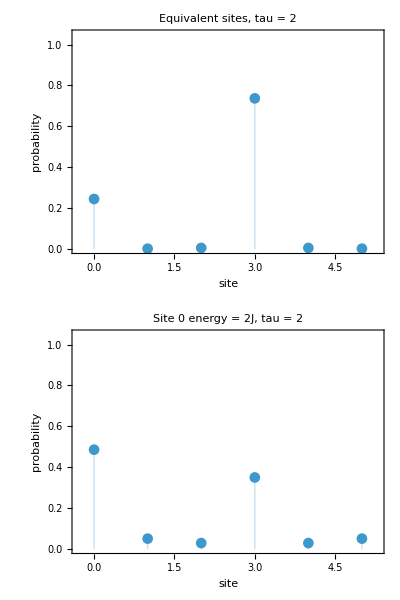

```mathematica
defectProbabilityAt[time_?NumericQ]:=Chop[Abs[MatrixExp[-ⅈ hDefect time].initial]^2];comparisonPlot={{probabilityPlot[probabilityAt[2],"Equivalent sites, tau = 2"]}, {probabilityPlot[defectProbabilityAt[2],"Site 0 energy = 2J, tau = 2"]}};comparisonPlot
```

Exercise: replace the number 2 in the defect energy by 0, then by a larger positive number. Predict how likely the particle is to remain near its initial site. A closed finite ring has unitary, recurrent dynamics; it is not an irreversible diffusion model.

At time 2, the Fourier-wave evolution agrees with the matrix exponential to within 10^-12 in every component.

```mathematica
Max[Abs[stateAt[2]-MatrixExp[-2  h0].initial]]<1/10^12
```

True

The defect of energy 2J breaks one-step translation symmetry: the commutator is nonzero.

```mathematica
Norm[hDefect.shift-shift.hDefect]>0
```

True

The sine wave with a node at site 0 remains an eigenstate with energy -J, even with the defect.

```mathematica
FullSimplify[defectiveHamiltonian.nodeState-J nodeState]
```

True

With the defect, total probability stays within 10^-12 of one at times from 0 to 4 in steps of 1/4.

```mathematica
Max[Abs[Table[Total[defectProbabilityAt[time]]-1,{time,0,4,1/4}]]]<1/10^12
```

True